## Ejemplo 2

### Lagrangiano

```mathematica
T[v1_,v2_,m_,Ι_]=1/2 m(v1)^2+1/2 Ι(v2)^2;
U[x1_,x2_,k_,l_]=1/2 k(x1+l x2)^2+1/2 k(x1-l x2)^2;
L[x1_,x2_,v1_,v2_,m_,k1_,k2_]=T[v1,v2,m,Ι]-U[x1,x2,k,l]
```

(m v1^2)/2-1/2 k (x1-l x2)^2-1/2 k (x1+l x2)^2+(v2^2 Ι)/2

### Matriz de potencial y de masa

```mathematica
v11=D[(D[U[x1,x2,k,l], x1]), x1];
v12=D[(D[U[x1,x2,k,l], x1]), x2];
v21=D[(D[U[x1,x2,k,l], x2]), x1];
v22=D[(D[U[x1,x2,k,l], x2]), x2];
V={{v11,v12},{v21,v22}}
MatrixForm[V]
```

{{2 k,0},{0,2 k l^2}}

(2 k | 0
0 | 2 k l^2)

```mathematica
m11=D[(D[T[v1,v2,m,Ι], v1]), v1];
m12=D[(D[T[v1,v2,m,Ι], v1]), v2];
m21=D[(D[T[v1,v2,m,Ι], v2]), v1];
m22=D[(D[T[v1,v2,m,Ι], v2]), v2];
M={{m11,m12},{m21,m22}}
MatrixForm[M]
```

{{m,0},{0,Ι}}

(m | 0
0 | Ι)

### Matriz secular

```mathematica
S[ω_]=V-ω^2 M;
MatrixForm[S[ω]]
```

(2 k-m ω^2 | 0
0 | 2 k l^2-Ι ω^2)

### Autovalores y autovectores (sin normalizar)

```mathematica
W1=Eigenvalues[S[ω]][[1]]
W2=Eigenvalues[S[ω]][[2]]
```

2 k-m ω^2

2 k l^2-Ι ω^2

```mathematica
ω1=ω/.Solve[W1==0,ω][[2]]
ω2=ω/.Solve[W2==0,ω][[2]]
```

(√2 √k)/(√m)

(√2 √k l)/(√Ι)

```mathematica
Eigenvectors[S[ω]]
r1=Eigenvectors[S[ω]][[1]]
r2=Eigenvectors[S[ω]][[2]]
```

{{1,0},{0,1}}

{1,0}

{0,1}

### Normalización

```mathematica
ρ1[α_]=α {r1};
ρ2[β_]=β {r2};
ρ1T[α_]=Transpose[ρ1[α]];
ρ2T[β_]=Transpose[ρ2[β]];
MatrixForm[ρ1[α]]
MatrixForm[ρ2[β]]
MatrixForm[ρ1T[α]]
MatrixForm[ρ2T[β]]
```

(α | 0)

(0 | β)

(α
0)

(0
β)

```mathematica
α1=α/.Solve[Dot[ρ1[α],M, ρ1T[α]]==1,α][[1]]
α2=α/.Solve[Dot[ρ1[α],M, ρ1T[α]]==1,α][[2]]
β1=β/.Solve[Dot[ρ2[β],M, ρ2T[β]]==1,β][[1]]
β2=β/.Solve[Dot[ρ2[β],M, ρ2T[β]]==1,β][[2]]
```

-1/(√m)

1/(√m)

-1/(√Ι)

1/(√Ι)

```mathematica
MatrixForm[Simplify[ρ1[α2]]]
MatrixForm[ρ2[β2]]
MatrixForm[ρ1T[α2]]
MatrixForm[ρ2T[β2]]
```

(1/(√m) | 0)

(0 | 1/(√Ι))

(1/(√m)
0)

(0
1/(√Ι))

### Matriz modal

```mathematica
𝒜={α2 r1,β2 r2}
MatrixForm[𝒜]
```

{{1/(√m),0},{0,1/(√Ι)}}

(1/(√m) | 0
0 | 1/(√Ι))

```mathematica
𝒜T=Transpose[𝒜]
MatrixForm[𝒜T]
```

{{1/(√m),0},{0,1/(√Ι)}}

(1/(√m) | 0
0 | 1/(√Ι))

```mathematica
MatrixForm[Dot[𝒜T,M,𝒜]]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[Dot[𝒜T,V,𝒜]]
```

((2 k)/m | 0
0 | (2 k l^2)/Ι)

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

### Desplazamientos

```mathematica
η[t_,C1_,C2_,ϕ1_,ϕ2_]=C1 ρ1T[α2] Cos[ω1 t+ϕ1]+C2 ρ2T[α2] Cos[ω2 t+ϕ2]
ηp[t_,C1_,C2_,ϕ1_,ϕ2_]=Simplify[D[η[t,C1,C2,ϕ1,ϕ2], t]]
```

{{(C1 Cos[(√2 √k t)/(√m)+ϕ1])/(√m)},{(C2 Cos[(√2 √k l t)/(√Ι)+ϕ2])/(√m)}}

{{-(√2 C1 √k Sin[(√2 √k t)/(√m)+ϕ1])/m},{-(√2 C2 √k l Sin[(√2 √k l t)/(√Ι)+ϕ2])/(√m √Ι)}}

Las coordenadas normales son:

```mathematica
ζ[t_,C1_,C2_,ϕ1_,ϕ2_]=Dot[𝒜T,M,η[t,C1,C2,ϕ1,ϕ2]]//Simplify
```

{{C1 Cos[(√2 √k t)/(√m)+ϕ1]},{(C2 √Ι Cos[(√2 √k l t)/(√Ι)+ϕ2])/(√m)}}

```mathematica
MatrixForm[{{C1 Cos[(√2 √k t)/(√m)+ϕ1]},{(C2 √Ι Cos[(√2 √k l t)/(√Ι)+ϕ2])/(√m)}}]
```

(C1 Cos[(√2 √k t)/(√m)+ϕ1]
(C2 √Ι Cos[(√2 √k l t)/(√Ι)+ϕ2])/(√m))

### Condiciones de contorno y ejemplos

#### Ejemplo 1

η1(0)=A; η2(0)=0; η̇ 1(0)=0; η̇ 2(0)=κ

```mathematica
η0={{A},{0}};
ηp0={{0},{κ}};
```

```mathematica
MatrixForm[η0]
MatrixForm[ηp0]
```

(A
0)

(0
κ)

```mathematica
Solve[η[0,C1,C2,ϕ1,ϕ2]==η0&&ηp[0,C1,C2,ϕ1,ϕ2]==ηp0,{C1,C2,ϕ1,ϕ2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{C1→-A √m,C2→-(√m √Ι κ)/(√2 √k l),ϕ1→-π,ϕ2→π/2},{C1→-A √m,C2→-(√m √Ι κ)/(√2 √k l),ϕ1→π,ϕ2→π/2},{C1→-A √m,C2→(√m √Ι κ)/(√2 √k l),ϕ1→-π,ϕ2→-π/2},{C1→-A √m,C2→(√m √Ι κ)/(√2 √k l),ϕ1→π,ϕ2→-π/2},{C1→A √m,C2→-(√m √Ι κ)/(√2 √k l),ϕ1→0,ϕ2→π/2},{C1→A √m,C2→(√m √Ι κ)/(√2 √k l),ϕ1→0,ϕ2→-π/2}}

Elegimos un conjunto de parámetros de los posibles, por ejemplo, la novena solución

```mathematica
%84⟦1⟧
```

{C1→-A √m,C2→-(√m √Ι κ)/(√2 √k l),ϕ1→-π,ϕ2→π/2}

```mathematica
η[t,-A √m,-(√m √Ι κ)/(√2 √k l),-π,π/2]
```

{{A Cos[(√2 √k t)/(√m)]},{(√Ι κ Sin[(√2 √k l t)/(√Ι)])/(√2 √k l)}}

Así, la solución para los desplazamientos

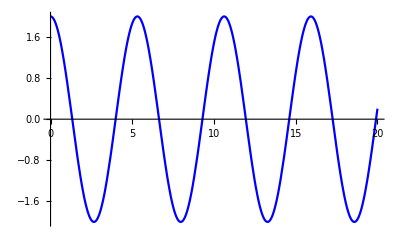

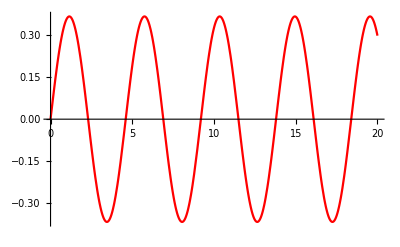

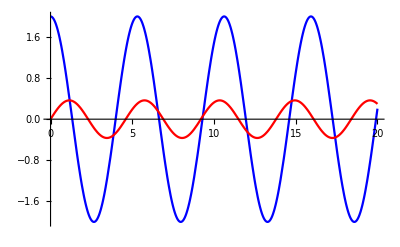

```mathematica
η1[t_,m_,k_,Ι_,l_,κ_,A_]=A Cos[(√2 √k t)/(√m)];
η2[t_,m_,k_,Ι_,l_,κ_,A_]=(√Ι κ Sin[(√2 √k l t)/(√Ι)])/(√2 √k l);
Plot[{η1[t,1,0.7,0.75,1,0.5,2]},{t,0,20},PlotStyle->Blue]
Plot[{η2[t,1,0.7,0.75,1,0.5,2]},{t,0,20},PlotStyle->Red]
Plot[{η1[t,1,0.7,0.75,1,0.5,2],η2[t,1,0.7,0.75,1,0.5,2]},{t,0,20},PlotStyle->{Blue,Red}]
```

#### Ejemplo 2

η1(0)=A; η2(0)=-A; η̇ 1(0)=0; η̇ 2(0)=0

```mathematica
η0={{A},{-A}};
ηp0={{0},{0}};
```

```mathematica
MatrixForm[η0]
```

(A
-A)

```mathematica
Solve[η[0,C1,C2,ϕ1,ϕ2]==η0&&ηp[0,C1,C2,ϕ1,ϕ2]==ηp0,{C1,C2,ϕ1,ϕ2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C1→0,C2→(-√2 A k1 √m-2 √2 A k2 √m)/(k1+2 k2),ϕ2→0},{C1→0,C2→(√2 A k1 √m+2 √2 A k2 √m)/(k1+2 k2),ϕ2→-π},{C1→0,C2→(√2 A k1 √m+2 √2 A k2 √m)/(k1+2 k2),ϕ2→π}}

```mathematica
%55⟦1⟧
```

{C1→0,C2→(-√2 A k1 √m-2 √2 A k2 √m)/(k1+2 k2),ϕ2→0}

```mathematica
η[t,0,(-√2 A k1 √m-2 √2 A k2 √m)/(k1+2 k2),π/4,0]//Simplify
```

{{A Cos[(√(k1+2 k2) t)/(√m)]},{-A Cos[(√(k1+2 k2) t)/(√m)]}}

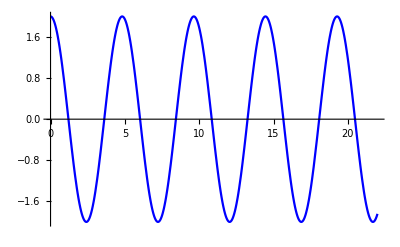

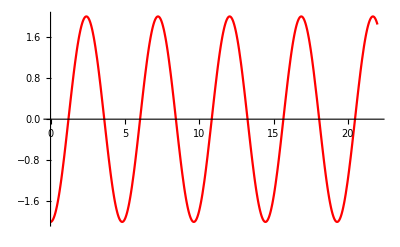

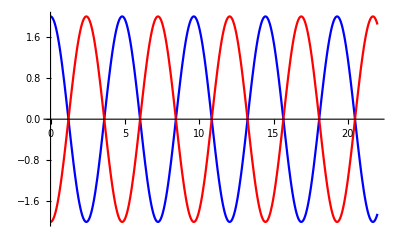

```mathematica
η1[t_,m_,k1_,k2_,A_]=A Cos[(√(k1+2 k2) t)/(√m)];
η2[t_,m_,k1_,k2_,A_]=-A Cos[(√(k1+2 k2) t)/(√m)];
Plot[{η1[t,1,0.7,0.5,2]},{t,0,7π},PlotStyle->Blue]
Plot[{η2[t,1,0.7,0.5,2]},{t,0,7π},PlotStyle->Red]
Plot[{η1[t,1,0.7,0.5,2],η2[t,1,0.7,0.5,2]},{t,0,7π},PlotStyle->{Blue,Red}]
```